# Homework 6 Cagatay Duygu - 48369962

## Given codes were used and edited for the homework. For Full state feedback, general procedure for multiple input system, repeated eigenvalue (k<=r), k=2 n = 5, r = 2 case should be used.

```mathematica
Quit[]
```

# b) Full State Feedback Design

```mathematica
A=({{-3, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {10, -6, -2, 0, 2}, {0, 0, 0, 0, 1}, {-6, 2, 0, -1, -6}});B=({{1, 0}, {0, 0}, {3, 1}, {0, 0}, {2, 1}});Cm=({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 1, 0}});Dm=({{0, 0}, {0, 0}, {0, 0}});
n=Dimensions[A][[1]];r=Dimensions[B][[2]]; m=3;
Eigenvalues[A]//N
```

{-5.52097,-2.00948+1.62082 ⅈ,-2.00948-1.62082 ⅈ,-1.29176,-0.168301}

#### Find Controllability matrix :

```mathematica
P=Join[B,A.B,A.A.B,A.A.A.B, A.A.A.A.B, 2];
Print["P = ",MatrixForm[P]]
Print["Rank of P: ",MatrixRank[P]]
If[MatrixRank[P]==n,Print["System is controllable."],Print["System is uncontrollable."]]
```

P = (1 | 0 | -3 | 0 | 12 | 1 | -28 | -3 | -16 | -9
0 | 0 | 3 | 1 | 8 | 0 | -100 | -18 | 532 | 120
3 | 1 | 8 | 0 | -100 | -18 | 532 | 120 | -2380 | -606
0 | 0 | 2 | 1 | -18 | -6 | 130 | 37 | -818 | -222
2 | 1 | -18 | -6 | 130 | 37 | -818 | -222 | 4746 | 1277)

Rank of P: 5

System is controllable.

#### Form X = [I λ - A ⋮ B] matrix and obtain the null space:

```mathematica
{λ1,λ2,λ3, λ4, λ5}={-3.,-4., -4., -5., -5.};
Imat=IdentityMatrix[n];Clear[λ];
X=Join[Imat λ-A,B,2]; Print["X = ",MatrixForm[X]]
U=NullSpace[X]ᵀ; Print["U = ",MatrixForm[U]]
```

X = (3+λ | -1 | 0 | 0 | 0 | 1 | 0
0 | λ | -1 | 0 | 0 | 0 | 0
-10 | 6 | 2+λ | 0 | -2 | 3 | 1
0 | 0 | 0 | λ | -1 | 0 | 0
6 | -2 | 0 | 1 | 6+λ | 2 | 1)

U = (-(1+8 λ+λ^2)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -((9+2 λ+λ^2) (1+6 λ+λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(3+25 λ+11 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(19+117 λ+41 λ^2+3 λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(3 λ+25 λ^2+11 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(λ (19+117 λ+41 λ^2+3 λ^3))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(8+14 λ+5 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 λ (9+2 λ+λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(8 λ+14 λ^2+5 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 (9 λ^2+2 λ^3+λ^4))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
0 | 1
1 | 0)

#### Form Ψ and ℱ matrices by partinioning U :

```mathematica
Ψ=Take[U,n];Print["Ψ = ",MatrixForm[Ψ]]
ℱ:=Take[U,-r];Print["ℱ = ",MatrixForm[ℱ]]
```

Ψ = (-(1+8 λ+λ^2)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -((9+2 λ+λ^2) (1+6 λ+λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(3+25 λ+11 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(19+117 λ+41 λ^2+3 λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(3 λ+25 λ^2+11 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(λ (19+117 λ+41 λ^2+3 λ^3))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(8+14 λ+5 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 λ (9+2 λ+λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(8 λ+14 λ^2+5 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 (9 λ^2+2 λ^3+λ^4))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5))

ℱ = (0 | 1
1 | 0)

#### Form composite matrices Ω = [Ψ (λ1) Ψ (λ2) ... Ψ (λn)] and Λ = [ℱ (λ1) ℱ (λ2) ... ℱ (λn)] :

```mathematica
Ω=Join[Ψ/.λ->λ1,Ψ/.λ->λ2,Ψ/.λ->λ3,Ψ/.λ->λ4,Ψ/.λ->λ5,2];Print["Ω = ",MatrixForm[Ω]]
Λ=Join[ℱ/.λ->λ1,ℱ/.λ->λ2,ℱ/.λ->λ3,ℱ/.λ->λ4,ℱ/.λ->λ5,2]//Simplify
Λ //MatrixForm
```

Ω = (0.318182 | 2.18182 | 0.144231 | 1.14423 | 0.144231 | 1.14423 | 0.12963 | 0.888889 | 0.12963 | 0.888889
0. | 1. | -0.144231 | -0.144231 | -0.144231 | -0.144231 | -0.259259 | -0.777778 | -0.259259 | -0.777778
0. | -3. | 0.576923 | 0.576923 | 0.576923 | 0.576923 | 1.2963 | 3.88889 | 1.2963 | 3.88889
0.363636 | 1.63636 | 0.307692 | 1.30769 | 0.307692 | 1.30769 | 0.574074 | 2.22222 | 0.574074 | 2.22222
-1.09091 | -4.90909 | -1.23077 | -5.23077 | -1.23077 | -5.23077 | -2.87037 | -11.1111 | -2.87037 | -11.1111)

{{0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,1,0}}

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

#### Form the G and 𝒥 matrices by selecting linearly independent columns, one for each eigenvalue:

```mathematica
ColumnChoice={1,8,4, 3, 7};
G=Ω[[All,ColumnChoice]];Print["G = ",MatrixForm[G]]
𝒥=Λ[[All,ColumnChoice]];Print["𝒥 = ",MatrixForm[𝒥]]
Print["|G| = ",Det[G]]
```

G = (0.318182 | 0.888889 | 1.14423 | 0.144231 | 0.12963
0. | -0.777778 | -0.144231 | -0.144231 | -0.259259
0. | 3.88889 | 0.576923 | 0.576923 | 1.2963
0.363636 | 2.22222 | 1.30769 | 0.307692 | 0.574074
-1.09091 | -11.1111 | -5.23077 | -1.23077 | -2.87037)

𝒥 = (0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1)

|G| = 0.000849845

#### Solve for K :

```mathematica
K=𝒥.Inverse[G];Print["K = ", MatrixForm[K]]
```

K = (5.32907×10^-15 | -7.04762 | -2.29524 | -3. | -1.
10. | 35.1429 | 13.8857 | 9. | 5.)

#### Test closed-loop eigenvalues :

```mathematica
Eigenvalues[A-B.K]
```

{-5.,-5.,-4.,-4.,-3.}

# c) State Feedback Simulation

```mathematica
x[t_]:={x1[t],x2[t],x3[t],x4[t],x5[t]}
u[t_]:={u1[t],u2[t]}
y[t_]:=Cm.x[t]
v[t_]:={v1[t],v2[t]};


Cr=Take[Cm,r];
F=Inverse[−Cr.Inverse[A−B.K].B];


EqStateFdbk=Thread[x'[t]==(A-B.K).x[t]+B.F.v[t]]//Chop; (* We'll use this one to plot. *)
TableForm[EqStateFdbk]
IC={x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0};
```

x1'[t]==60. v1[t]-35.0476 v2[t]-3. x1[t]+8.04762 x2[t]+2.29524 x3[t]+3. x4[t]+1. x5[t]
x2'[t]==1. x3[t]
x3'[t]==20. v2[t]-20. x2[t]-9. x3[t]
x4'[t]==1. x5[t]
x5'[t]==-60. v1[t]+55.0476 v2[t]-16. x1[t]-19.0476 x2[t]-9.29524 x3[t]-4. x4[t]-9. x5[t]

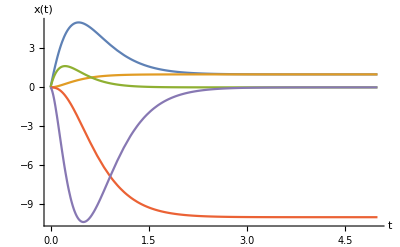

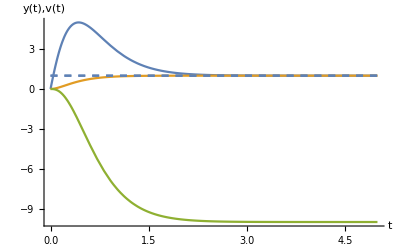

```mathematica
tmax=5;
DesInput={v1[t]->UnitStep[t],v2[t]->UnitStep[t]};
SFResp=NDSolve[{EqStateFdbk/.DesInput,IC},x[t],{t,0,tmax}];
Plot[Evaluate[x[t]/.SFResp],{t,0,tmax},AxesLabel->{"t","x(t)"},PlotRange->All]
yo=Plot[Evaluate[y[t]/.SFResp],{t,0,tmax},AxesLabel->{"t","y(t),v(t)"},PlotRange->All];
yd=Plot[{v1[t],v2[t]}/.DesInput,{t,0,tmax},PlotStyle->Dashed,PlotRange->All];
Show[yo,yd]
```

```mathematica
Quit[]
```

# d) Output State Feedback

## Algorithm for General Procedure multiple input system should be used. n = 5, r=2, k = 2, D=0

System is controllable (showed in the first part)

```mathematica
X=Join[Imat λ - A,B,2];MatrixForm[X];
U=NullSpace[X]ᵀ;MatrixForm[U];
Ψ=Take[U,n];MatrixForm[Ψ];
ℱp=Take[U,-r];MatrixForm[ℱp];
Ω=Join[Ψ/.λ->λ1,Ψ/.λ->λ2,Ψ/.λ->λ3,Ψ/.λ->λ4,Ψ/.λ->λ5,2];
MatrixForm[Ω]//N;
Ωp=Cm.Ω;Print["Ω'=",MatrixForm[Ωp]//N]
Λp=Join[ℱp/.λ->λ1,ℱp/.λ->λ2,ℱp/.λ->λ3,ℱp/.λ->λ4,ℱp/.λ->λ5,2];
Print["Λ'=",MatrixForm[Λp]]
```

Ω'=(0.318182 | 2.18182 | 0.144231 | 1.14423 | 0.144231 | 1.14423 | 0.12963 | 0.888889 | 0.12963 | 0.888889
0. | 1. | -0.144231 | -0.144231 | -0.144231 | -0.144231 | -0.259259 | -0.777778 | -0.259259 | -0.777778
0.363636 | 1.63636 | 0.307692 | 1.30769 | 0.307692 | 1.30769 | 0.574074 | 2.22222 | 0.574074 | 2.22222)

Λ'=(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

```mathematica
ColumnChoice2={1,4,7};
Gp=Ωp[[All,ColumnChoice2]];MatrixForm[Gp]//N
```

(0.318182 | 1.14423 | 0.12963
0. | -0.144231 | -0.259259
0.363636 | 1.30769 | 0.574074)

```mathematica
𝒥p=Λp[[All,ColumnChoice2]];MatrixForm[𝒥p]
```

(0 | 1 | 0
1 | 0 | 1)

```mathematica
Det[Gp]//N
```

-0.0195464

```mathematica
Kstar=𝒥p.Inverse[Gp]//N; Kstar // MatrixForm
```

(4.82319 | -6.93333 | -4.22029
-15.7921 | 24.9333 | 16.5681)

```mathematica
Eigenvalues[A-B.Kstar.Cm]//N
```

{-5.,-4.,-3.55052,-3.,-0.272669}

Only 3 of the desired eigenvalues can be obtained as expected.

# d) Output feedback simulation:

```mathematica
Imm=IdentityMatrix[m];
Imr=IdentityMatrix[r];
x[t_]:={x1[t],x2[t],x3[t],x4[t],x5[t]};
Fp=Inverse[−Cr.Inverse[A−B.Kstar.Cm].B];
v[t_]:={v1[t],v2[t]};
```

```mathematica
EqOutFdbk=Thread[x'[t]==(A-B.Kstar.Cm).x[t]+(B.Fp).v[t]]//Chop;
y[t_]:=Cm.x[t]
TableForm[EqOutFdbk]
```

x1'[t]==88.0087 v1[t]-45.9159 v2[t]-7.82319 x1[t]+7.93333 x2[t]+4.22029 x4[t]
x2'[t]==1. x3[t]
x3'[t]==-85.5602 v1[t]+45.2986 v2[t]+11.3226 x1[t]-10.1333 x2[t]-2. x3[t]-3.90725 x4[t]+2. x5[t]
x4'[t]==1. x5[t]
x5'[t]==-173.569 v1[t]+91.2145 v2[t]+0.145756 x1[t]-9.06667 x2[t]-9.12754 x4[t]-6. x5[t]

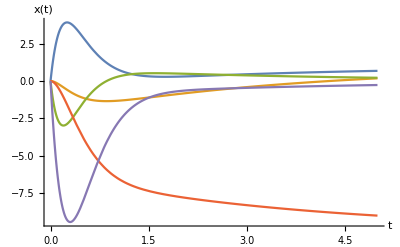

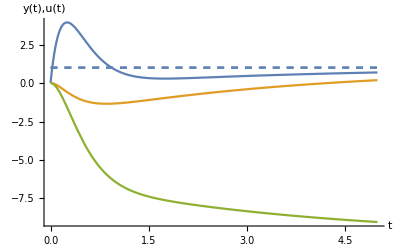

```mathematica
OFResp=NDSolve[{EqOutFdbk/.DesInput,IC},x[t],{t,0,tmax}];
Plot[Evaluate[x[t]/.OFResp],{t,0,tmax},AxesLabel->{"t","x(t)"},PlotRange->All]
yo=Plot[Evaluate[y[t]/.OFResp],{t,0,tmax},AxesLabel->{"t","y(t),u(t)"},PlotRange->All];
Show[yo,yd]
```

It is not as efficient as full state feedback since unplaced eigenvalues is slower than the desired ones. If I select different columns I can get:

```mathematica
ColumnChoice2={1,4,10};
Gp=Ωp[[All,ColumnChoice2]];MatrixForm[Gp]//N
```

(0.318182 | 1.14423 | 0.888889
0. | -0.144231 | -0.777778
0.363636 | 1.30769 | 2.22222)

```mathematica
𝒥p=Λp[[All,ColumnChoice2]];MatrixForm[𝒥p]
```

(0 | 1 | 1
1 | 0 | 0)

```mathematica
Det[Gp]//N
```

-0.0553613

```mathematica
Kstar=𝒥p.Inverse[Gp]//N; Kstar // MatrixForm
```

(4.1614 | -6.93333 | -3.64123
-12.5825 | 24.9333 | 13.7596)

```mathematica
Eigenvalues[A-B.Kstar.Cm]//N
```

{-5.,-4.,-3.,-2.31125,-0.85015}

```mathematica
Imm=IdentityMatrix[m];
Imr=IdentityMatrix[r];
x[t_]:={x1[t],x2[t],x3[t],x4[t],x5[t]};
Fp=Inverse[−Cr.Inverse[A−B.Kstar.Cm].B];
v[t_]:={v1[t],v2[t]};
```

```mathematica
EqOutFdbk=Thread[x'[t]==(A-B.Kstar.Cm).x[t]+(B.Fp).v[t]]//Chop;
y[t_]:=Cm.x[t]
TableForm[EqOutFdbk]
```

x1'[t]==76.3447 v1[t]-40.7044 v2[t]-7.1614 x1[t]+7.93333 x2[t]+3.64123 x4[t]
x2'[t]==1. x3[t]
x3'[t]==-63.9816 v1[t]+35.657 v2[t]+10.0982 x1[t]-10.1333 x2[t]-2. x3[t]-2.83596 x4[t]+2. x5[t]
x4'[t]==1. x5[t]
x5'[t]==-140.326 v1[t]+76.3614 v2[t]-1.74035 x1[t]-9.06667 x2[t]-7.47719 x4[t]-6. x5[t]

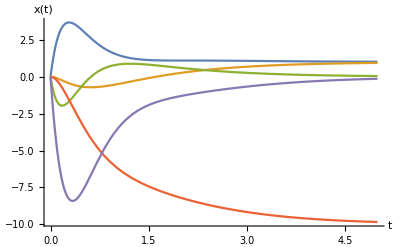

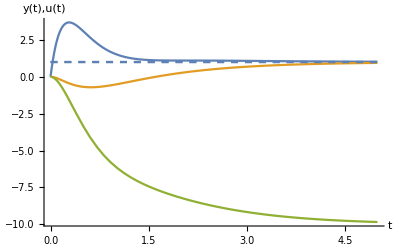

```mathematica
OFResp=NDSolve[{EqOutFdbk/.DesInput,IC},x[t],{t,0,tmax}];
Plot[Evaluate[x[t]/.OFResp],{t,0,tmax},AxesLabel->{"t","x(t)"},PlotRange->All]
yo=Plot[Evaluate[y[t]/.OFResp],{t,0,tmax},AxesLabel->{"t","y(t),u(t)"},PlotRange->All];
Show[yo,yd]
```

This one gives a better result because of faster eigenvalues. Some column selection may have cause unstability because of positive eigenvectors.

# f) Full State Observer

```mathematica
Q=Join[Cmᵀ,Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Cmᵀ,2];
Print["Q = ",MatrixForm[Q]]
If[MatrixRank[Q]==n,Print["System is observable."],Print["System is uncontrollable."]]
```

Q = (1 | 0 | 0 | -3 | 0 | 0 | 9 | 10 | -6
0 | 1 | 0 | 1 | 0 | 0 | -3 | -6 | 2
0 | 0 | 0 | 0 | 1 | 0 | 1 | -2 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -6)

System is observable.

```mathematica
{λo1,λo2,λo3, λo4,λo5}={-10,-12,-14,-16,-20}; 
Xo=Join[Imat λ-Aᵀ,Cmᵀ,2]; MatrixForm[Xo]
Uo=NullSpace[Xo]ᵀ//Simplify; MatrixForm[Uo]
```

(3+λ | 0 | -10 | 0 | 6 | 1 | 0 | 0
-1 | λ | 6 | 0 | -2 | 0 | 1 | 0
0 | -1 | 2+λ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | λ | 1 | 0 | 0 | 1
0 | 0 | -2 | -1 | 6+λ | 0 | 0 | 0)

((2 (8+6 λ+3 λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 (5+24 λ+5 λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(6+34 λ+19 λ^2+8 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(2 λ (2+λ))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -((3+λ) (2+13 λ+8 λ^2+λ^3))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2+13 λ+8 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(2 λ)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -((3+λ) (1+6 λ+λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(1+6 λ+λ^2)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(48+76 λ+42 λ^2+11 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | (2 (3+λ))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | 2/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(8+12 λ+5 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 λ (3+λ))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 λ)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)

```mathematica
Ψo=Take[Uo,n];MatrixForm[Ψo]
```

((2 (8+6 λ+3 λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 (5+24 λ+5 λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(6+34 λ+19 λ^2+8 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(2 λ (2+λ))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -((3+λ) (2+13 λ+8 λ^2+λ^3))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2+13 λ+8 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(2 λ)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -((3+λ) (1+6 λ+λ^2))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(1+6 λ+λ^2)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(48+76 λ+42 λ^2+11 λ^3+λ^4)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | (2 (3+λ))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | 2/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5)
-(8+12 λ+5 λ^2+λ^3)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 λ (3+λ))/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5) | -(2 λ)/(8+60 λ+81 λ^2+43 λ^3+11 λ^4+λ^5))

```mathematica
ℱo:=Take[Uo,-m];MatrixForm[ℱo]
```

(0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)

```mathematica
Ωo=Join[Ψo/.λ->λo1,Ψo/.λ->λo2,Ψo/.λ->λo3,Ψo/.λ->λo4,Ψo/.λ->λo5,2];Print["Ωo=",MatrixForm[Ωo]//N]
```

Ωo=(-0.0194571 | 0.0207908 | 0.139887 | -0.00875274 | 0.0103939 | 0.109956 | -0.00469303 | 0.00594878 | 0.0903683 | -0.00280978 | 0.00372296 | 0.0766367 | -0.00124145 | 0.00174008 | 0.0587212
0.00627648 | 0.0900675 | -0.0128668 | 0.00285415 | 0.0781324 | -0.00868138 | 0.0015399 | 0.0683606 | -0.0062146 | 0.000925574 | 0.0605383 | -0.00465679 | 0.000410773 | 0.0490566 | -0.00288568
-0.00078456 | -0.0112584 | 0.00160835 | -0.000285415 | -0.00781324 | 0.000868138 | -0.000128325 | -0.00569671 | 0.000517883 | -0.0000661124 | -0.00432417 | 0.000332628 | -0.0000228207 | -0.00272537 | 0.000160316
0.0975992 | 0.000549192 | -0.000078456 | 0.0821996 | 0.000214061 | -0.0000237846 | 0.0707987 | 0.000100827 | -9.16607×10^-6 | 0.0621126 | 0.0000537163 | -4.13203×10^-6 | 0.0498222 | 0.0000193976 | -1.14104×10^-6
-0.0240075 | 0.00549192 | -0.00078456 | -0.0136048 | 0.00256874 | -0.000285415 | -0.00881776 | 0.00141157 | -0.000128325 | -0.00619804 | 0.000859462 | -0.0000661124 | -0.00355547 | 0.000387952 | -0.0000228207)

```mathematica
Λo=Join[ℱo/.λ->λo1,ℱo/.λ->λo2,ℱo/.λ->λo3,ℱo/.λ->λo4,ℱo/.λ->λo5,2];Print["Λo=",MatrixForm[Λo]]
```

Λo=(0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0)

```mathematica
ColumnChoiceo={1,5,9,14,10};
Go=Ωo[[All,ColumnChoiceo]];MatrixForm[Go]//N
𝒥o = Λo[[All,ColumnChoiceo]];MatrixForm[𝒥o]
Det[Go]//N
```

(-0.0194571 | 0.0103939 | 0.0903683 | 0.00174008 | -0.00280978
0.00627648 | 0.0781324 | -0.0062146 | 0.0490566 | 0.000925574
-0.00078456 | -0.00781324 | 0.000517883 | -0.00272537 | -0.0000661124
0.0975992 | 0.000214061 | -9.16607×10^-6 | 0.0000193976 | 0.0621126
-0.0240075 | 0.00256874 | -0.000128325 | 0.000387952 | -0.00619804)

(0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1)

1.39926×10^-8

```mathematica
L=(𝒥o.Inverse[Go]//Chop)ᵀ;
MatrixForm[L] // FullSimplify //N
```

(10.9953 | 1.06857 | -0.00821362
0.664991 | 29.976 | 0.965242
17.2498 | 173.43 | 23.1023
-0.710525 | -0.140849 | 20.0287
-12.1896 | 0.730585 | 39.2742)

```mathematica
Ac=A-L.Cm;MatrixForm[Ac]//Chop // N
```

(-13.9953 | -0.0685687 | 0. | 0.00821362 | 0.
-0.664991 | -29.976 | 1. | -0.965242 | 0.
-7.24984 | -179.43 | -2. | -23.1023 | 2.
0.710525 | 0.140849 | 0. | -20.0287 | 1.
6.18965 | 1.26941 | 0. | -40.2742 | -6.)

```mathematica
Eigenvalues[A-L.Cm]
```

{-20,-16,-14,-12,-10}

# g) Full State Observer Simulation

```mathematica
xo[t_]:={xo1[t],xo2[t],xo3[t],xo4[t],xo5[t]};
u[t_]:={u1[t],u2[t]};
EqObserver=Thread[xo'[t]==Ac.xo[t]+L.y[t]+B.u[t]]//Chop  //N
```

{xo1'[t]==u1[t]+10.9953 x1[t]+1.06857 x2[t]-0.00821362 x4[t]-13.9953 xo1[t]-0.0685687 xo2[t]+0.00821362 xo4[t],xo2'[t]==0.664991 x1[t]+29.976 x2[t]+0.965242 x4[t]-0.664991 xo1[t]-29.976 xo2[t]+xo3[t]-0.965242 xo4[t],xo3'[t]==3. u1[t]+u2[t]+17.2498 x1[t]+173.43 x2[t]+23.1023 x4[t]-7.24984 xo1[t]-179.43 xo2[t]-2. xo3[t]-23.1023 xo4[t]+2. xo5[t],xo4'[t]==-0.710525 x1[t]-0.140849 x2[t]+20.0287 x4[t]+0.710525 xo1[t]+0.140849 xo2[t]-20.0287 xo4[t]+xo5[t],xo5'[t]==2. u1[t]+u2[t]-12.1896 x1[t]+0.730585 x2[t]+39.2742 x4[t]+6.18965 xo1[t]+1.26941 xo2[t]-40.2742 xo4[t]-6. xo5[t]}

```mathematica
EqFullObsFdbk=Thread[x'[t]==A.x[t]-B.K.xo[t]+B.F.v[t]];
u[t_]:=F.v[t]-K.xo[t]
EqObserver2=Thread[xo'[t]==Ac.xo[t]+L.y[t]+B.u[t]];
y[t_]:=Cm.x[t]
TableForm[{EqFullObsFdbk,EqObserver2}//Flatten //N]
```

x1'[t]==60. v1[t]-35.0476 v2[t]-3. x1[t]+x2[t]-5.32907×10^-15 xo1[t]+7.04762 xo2[t]+2.29524 xo3[t]+3. xo4[t]+1. xo5[t]
x2'[t]==0.+x3[t]
x3'[t]==-1.42109×10^-12 v1[t]+20. v2[t]+10. x1[t]-6. x2[t]-2. x3[t]+2. x5[t]-10. xo1[t]-14. xo2[t]-7. xo3[t]-6.57252×10^-14 xo4[t]-2. xo5[t]
x4'[t]==0.+x5[t]
x5'[t]==-60. v1[t]+55.0476 v2[t]-6. x1[t]+2. x2[t]-1. x4[t]-6. x5[t]-10. xo1[t]-21.0476 xo2[t]-9.29524 xo3[t]-3. xo4[t]-3. xo5[t]
xo1'[t]==60. v1[t]-35.0476 v2[t]+10.9953 x1[t]+1.06857 x2[t]-0.00821362 x4[t]-13.9953 xo1[t]+6.97905 xo2[t]+2.29524 xo3[t]+3.00821 xo4[t]+1. xo5[t]
xo2'[t]==0.664991 x1[t]+29.976 x2[t]+0.965242 x4[t]-0.664991 xo1[t]-29.976 xo2[t]+xo3[t]-0.965242 xo4[t]
xo3'[t]==-180. v1[t]+125.143 v2[t]+17.2498 x1[t]+173.43 x2[t]+23.1023 x4[t]-17.2498 xo1[t]-214.573 xo2[t]-15.8857 xo3[t]-32.1023 xo4[t]+3. (60. v1[t]-35.0476 v2[t]-5.32907×10^-15 xo1[t]+7.04762 xo2[t]+2.29524 xo3[t]+3. xo4[t]+1. xo5[t])-3. xo5[t]
xo4'[t]==-0.710525 x1[t]-0.140849 x2[t]+20.0287 x4[t]+0.710525 xo1[t]+0.140849 xo2[t]-20.0287 xo4[t]+xo5[t]
xo5'[t]==-180. v1[t]+125.143 v2[t]-12.1896 x1[t]+0.730585 x2[t]+39.2742 x4[t]-3.81035 xo1[t]-33.8734 xo2[t]-13.8857 xo3[t]-49.2742 xo4[t]+2. (60. v1[t]-35.0476 v2[t]-5.32907×10^-15 xo1[t]+7.04762 xo2[t]+2.29524 xo3[t]+3. xo4[t]+1. xo5[t])-11. xo5[t]

```mathematica
ICo={xo1[0]==0,xo2[0]==0,xo3[0]==0,xo4[0]==0,xo5[0]==0};
FullObsFdbkResponse=NDSolve[{EqFullObsFdbk/.DesInput, IC ,EqObserver2/.DesInput,ICo},{x[t],xo[t]}//Flatten,{t,0,tmax}];
```

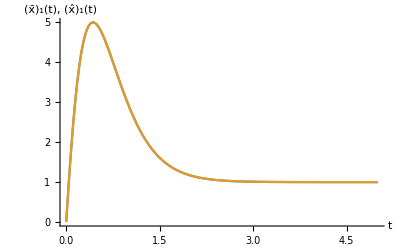

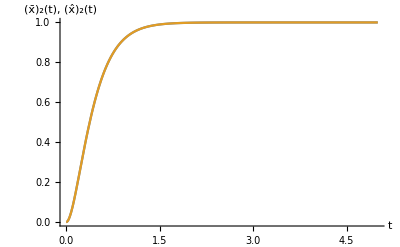

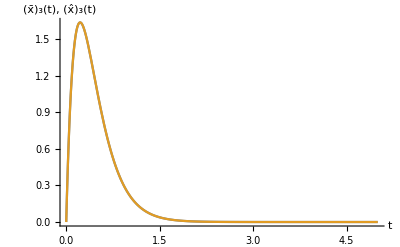

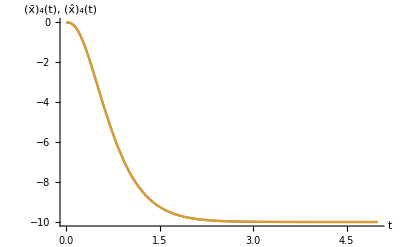

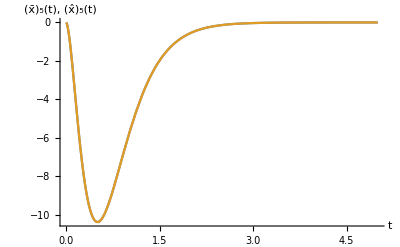

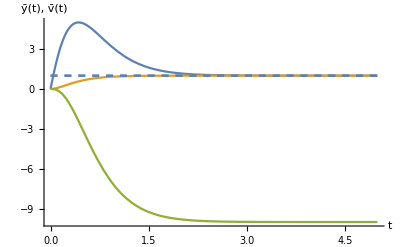

```mathematica
Plot[Evaluate[{x1[t],xo1[t]}/.FullObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_1(t), (x̂)_1(t)"}, PlotRange->All]
Plot[Evaluate[{x2[t],xo2[t]}/.FullObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_2(t), (x̂)_2(t)"}, PlotRange->All]
Plot[Evaluate[{x3[t],xo3[t]}/.FullObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_3(t), (x̂)_3(t)"}, PlotRange->All]
Plot[Evaluate[{x4[t],xo4[t]}/.FullObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_4(t), (x̂)_4(t)"}, PlotRange->All]
Plot[Evaluate[{x5[t],xo5[t]}/.FullObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_5(t), (x̂)_5(t)"}, PlotRange->All]
yo=Plot[Evaluate[y[t]/.FullObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","ȳ(t), v̄(t)"}, PlotRange->All];
Show[yo,yd]
```

# h) Reduced Order Observer Design:

```mathematica
We can measure m=3 states.   n - m states that should be estimated:
```

```mathematica
{λr1,λr2}={λo4,λo5} (*-20 and -16 were selected *)
```

{-16,-20}

```mathematica
Partition :
```

```mathematica
Print["x = ",MatrixForm[x[t]]]
xs1[t_]:=x[t][[{1,2,3}]];
xs2[t_]:=x[t][[{4,5}]];
Print["Xs1 = ",MatrixForm[xs1[t]],"\t xs2 = ",MatrixForm[xs2[t]]]
Print["A = ",MatrixForm[A]]
```

x = (x1[t]
x2[t]
x3[t]
x4[t]
x5[t])

Xs1 = (x1[t]
x2[t]
x3[t])	 xs2 = (x4[t]
x5[t])

A = (-3 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
10 | -6 | -2 | 0 | 2
0 | 0 | 0 | 0 | 1
-6 | 2 | 0 | -1 | -6)

```mathematica
A11=Take[A,m,m]; MatrixForm[A11]
```

(-3 | 1 | 0
0 | 0 | 1
10 | -6 | -2)

```mathematica
A12=Take[A,m,{m+1,n}];MatrixForm[A12]
```

(0 | 0
0 | 0
0 | 2)

```mathematica
A21=Take[A,{m+1,n},m];MatrixForm[A21]
```

(0 | 0 | 0
-6 | 2 | 0)

```mathematica
A22=Take[A,{m+1,n},{m+1,n}];MatrixForm[A22]
```

(0 | 1
-1 | -6)

```mathematica
B1=Take[B,m]; MatrixForm[B1]
```

(1 | 0
0 | 0
3 | 1)

```mathematica
B2=B[[{4,5},{1,2}]];  MatrixForm[B2]
```

(0 | 0
2 | 1)

```mathematica
Ir=IdentityMatrix[n-m];
Xr=Join[Ir λ-A22ᵀ,A12ᵀ,2];MatrixForm[Xr];
Ur = NullSpace[Xr]ᵀ//Simplify;
MatrixForm[Ur];
Ψr=Take[Ur,n-m];MatrixForm[Ψr];
ℱr:=Take[Ur,-m];MatrixForm[ℱr];
Ωr=Join[Ψr/.λ->λr1,Ψr/.λ->λr2,2];Print["Ωr =", MatrixForm[Ωr]]
Λr=Join[ℱr/.λ->λr1,ℱr/.λ->λr2,2];Print["Λr =", MatrixForm[Λr]]
```

Ωr =(2/161 | 0 | 0 | 2/281 | 0 | 0
32/161 | 0 | 0 | 40/281 | 0 | 0)

Λr =(0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0)

```mathematica
ColumnChoice={1,4};
Gr=Ωr[[All,ColumnChoice]];MatrixForm[Gr]
𝒥r=Λr[[All,ColumnChoice]];MatrixForm[𝒥r]
Det[Gr]//N
```

(2/161 | 2/281
32/161 | 40/281)

(0 | 0
0 | 0
1 | 1)

0.000353662

```mathematica
Lr=Transpose[𝒥r.Inverse[Gr]];
MatrixForm[Lr]
```

(0 | 0 | -319/2
0 | 0 | 15)

```mathematica
Ar=A22-Lr.A12; MatrixForm[Ar];
Eigenvalues[Ar]
```

{-20,-16}

# i) Reduced Order Observer Simulation:

```mathematica
Clear[u]
xro[t_]:={xro3[t], xro5[t]}
xhat[t_]:={xs1[t],xro[t]}//Flatten
u[t_]:=F.v[t]-K.xhat[t]
yr[t_]:= xs1'[t]-A11.xs1[t]-B1.u[t]
zr[t_]:=A21.xs1[t]+B2.u[t]

EqRedObsFdbk=Thread[x'[t]==A.x[t]-B.K.xhat[t]+B.F.v[t]];
u[t_]:=F.v[t]-K.xhat[t]
EqRedObserver=Thread[xro'[t]==Ar.xro[t]+Lr.yr[t]+zr[t]];
ICro={xro3[0]==0,xro5[0]==0}; 
y[t_]:=Cm.x[t]      
TableForm[{EqRedObsFdbk,EqRedObserver}//Flatten]
```

x1'[t]==60. v1[t]-35.0476 v2[t]-3. x1[t]+8.04762 x2[t]+2.29524 x3[t]+3. xro3[t]+1. xro5[t]
x2'[t]==0.+x3[t]
x3'[t]==-1.42109×10^-12 v1[t]+20. v2[t]+1.33227×10^-13 x1[t]-20. x2[t]-9. x3[t]+2 x5[t]-6.57252×10^-14 xro3[t]-2. xro5[t]
x4'[t]==0.+x5[t]
x5'[t]==-60. v1[t]+55.0476 v2[t]-16. x1[t]-19.0476 x2[t]-9.29524 x3[t]-x4[t]-6 x5[t]-3. xro3[t]-3. xro5[t]
xro3'[t]==320 xro5[t]-319/2 (180. v1[t]-125.143 v2[t]-1.49214×10^-13 x1[t]+41.1429 x2[t]+15.8857 x3[t]+9. xro3[t]-3 (60. v1[t]-35.0476 v2[t]-5.32907×10^-15 x1[t]+7.04762 x2[t]+2.29524 x3[t]+3. xro3[t]+1. xro5[t])+5. xro5[t]+x3'[t])
xro5'[t]==-180. v1[t]+125.143 v2[t]-16. x1[t]-33.1429 x2[t]-13.8857 x3[t]-10. xro3[t]+2 (60. v1[t]-35.0476 v2[t]-5.32907×10^-15 x1[t]+7.04762 x2[t]+2.29524 x3[t]+3. xro3[t]+1. xro5[t])-41. xro5[t]+15 (180. v1[t]-125.143 v2[t]-1.49214×10^-13 x1[t]+41.1429 x2[t]+15.8857 x3[t]+9. xro3[t]-3 (60. v1[t]-35.0476 v2[t]-5.32907×10^-15 x1[t]+7.04762 x2[t]+2.29524 x3[t]+3. xro3[t]+1. xro5[t])+5. xro5[t]+x3'[t])

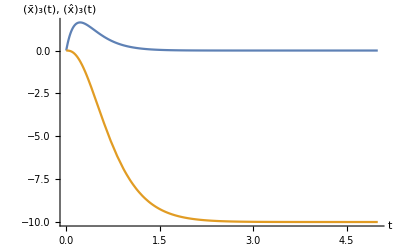

-Graphics-

-Graphics-

```mathematica
RedObsFdbkResponse=NDSolve[{EqRedObsFdbk/.DesInput, IC ,EqRedObserver/.DesInput,ICro},{x[t],xro3[t],xro5[t]}//Flatten,{t,0,tmax}];

Plot[Evaluate[{x3[t],xro3[t]}/.RedObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_3(t), (x̂)_3(t)"}, PlotRange->All]
Plot[Evaluate[{x5[t],xro5[t]}/.RedObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_5(t), (x̂)_5(t)"}, PlotRange->All]
yro=Plot[Evaluate[y[t]/. RedObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","ȳ(t), v̄(t)"}, PlotRange->All];
Show[yro ,yd]
```